# Atom-cavity interactions

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[PolarPlot,PolarAxes->True,PolarGridLines->Automatic,PolarTicks->{Drop[Table[i,{i,0,2 Pi,Pi/4}],-1],Automatic},LabelStyle->Directive[Black, 16],ImageSize->Medium];
```

## Single atom in a cavity - system characterization

### Mark’s example 1 - short confocal resonator

Algebra confirmed by hand, results agree with Mark if 87 RbD1 line assumed.

```mathematica
(*CAVITY PARAMS*)
L=1.5*^-4;(*cavity length*)
RoC = L;
F =3*^4;(* (π (R1 R2)^(1/4))/(1-(R1 R2)^(1/2))cavity finesse*)
FSR = c/(2L);(*free spectral range*)
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = 4.3*^-6;(*Confocal waist*)
V = (π w0^2 L)/2;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/2π}
(*ATOM PARAMS*)
d = 2.992 e a0/√2; (*D1*)
Γ = 2π 5.746*^6;(*ΓD2*); (*atom decay rate, e.g. 87Rb 5P3/2*)
λ = 7.95*^-7;(*λD2*);
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, confocal [dimensionless]:"
Cooperativity = 8/(ℏ ϵ0)(d^2 F)/(Γ λ^2 L)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)
```

Cavity w0, L, F, FSR, κ/(2π):

{4.3×10^-6,0.00015,30000,9.99567×10^11,3.28844×10^8}

Atom d [a.u.], Γ/(2π), λ:

{2.11566,5.746×10^6,7.95×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

4.87596×10^7

Cooperativity, confocal [dimensionless]:

24.1965

Fractional emission into cavity mode:

0.979754

Quantum efficiency:

0.835644

Compare w/ Mark’s result:

```mathematica
Cooperativity/23.9
```

1.0124

```mathematica
g/(2π 4.92*^7)
```

0.991048

### Short confocal resonator - medium finesse

Parameters for “gen 3” of the fiber Fabry-Perot built by the Goldsmith group

```mathematica
(*CAVITY PARAMS*)
L=1.2*^-4;(*cavity length*)
RoC = 2.475*^-4;(*ablated fiber mirror radius of curvature*)
F =8.3*^3;(*cavity finesse, measured by Garrett 2019.07.26*)
FSR = c/(2L);(*free spectral range*)
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = √((λ L)/(2 π));(*Confocal waist*)
V = (π w0^2 L)/2;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/2π}
(*ATOM PARAMS*)
d = D2MatElem; 
Γ =ΓD2; (*atom decay rate, e.g. 87Rb 5P3/2*)
λ =λD2;
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, confocal [dimensionless]:"
Cooperativity = 8/(ℏ ϵ0)(d^2 F)/(Γ λ^2 L)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)
```

Cavity w0, L, F, FSR, κ/(2π):

{3.86025×10^-6,0.00012,8300.,1.24946×10^12,1.48574×10^9}

Atom d [a.u.], Γ/(2π), λ:

{4.2344,6.0659×10^6,7.80241×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

1.22683×10^8

Cooperativity, confocal [dimensionless]:

32.9653

Fractional emission into cavity mode:

0.985059

Quantum efficiency:

0.946904

```mathematica
(g/Γ)^2
```

409.049

```mathematica
g^2/(κ Γ)
```

16.4827

### Short confocal resonator - low finesse

Parameters for “gen 3” of the fiber Fabry-Perot built by the Goldsmith group

```mathematica
(*CAVITY PARAMS*)
L=1.2*^-4;(*cavity length*)
RoC = 2.475*^-4;(*ablated fiber mirror radius of curvature*)
F =1*^3;(*cavity finesse, measured by Garrett 2019.07.26*)
FSR = c/(2L);(*free spectral range*)
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = √((λ L)/(2 π));(*Confocal waist*)
V = (π w0^2 L)/2;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/2π}
(*ATOM PARAMS*)
d = D2MatElem; 
Γ =ΓD2; (*atom decay rate, e.g. 87Rb 5P3/2*)
λ =λD2;
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, confocal [dimensionless]:"
Cooperativity = 8/(ℏ ϵ0)(d^2 F)/(Γ λ^2 L)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)
```

Cavity w0, L, F, FSR, κ/(2π):

{0.00437019 √λ,0.00012,1000,1.24946×10^12,1.23317×10^10}

Atom d [a.u.], Γ/(2π), λ:

{4.2344,6.0659×10^6,7.80241×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

1.22683×10^8

Cooperativity, confocal [dimensionless]:

3.97173

Fractional emission into cavity mode:

0.888186

Quantum efficiency:

0.883895

```mathematica
(g/Γ)^2
```

409.049

### Cooperativity Trade-off

See Meschede paper “Strong Purcell effect on a neutral atom....”. Note that what follows applies specifically to the case of equilibrium when an atom in a cavity is being driven continuously with an external field of Rabi freq. Ω.

```mathematica
coop = g^2/(2κ γ);
Ccoop = g^2/(2(κ-ⅈ Δc)(γ-ⅈ Δa));(*complex coop. see supplemental*)
Rfs=Ω^2/(2γ(1+Δa^2/γ^2))1/((1+2Ccoop)*conj[(1+2Ccoop)]);
Rc = (Ω^2 Ccoop*conj[Ccoop])/(γ coop(1+2 Ccoop)*conj[(1+2Ccoop)]);
```

```mathematica
Δa = Δc=0; (*cavity on tuned to atomic resonance, and probe tuned to cavity resonance
*)
```

```mathematica
Rfs
```

Ω^2/(2 γ (1+g^2/(γ κ))^2)

```mathematica
Rc
```

(g^2 Ω^2)/(2 γ^2 (1+g^2/(γ κ))^2 κ)

```mathematica
Clear[coop];
(Rfs+Rc)/.g^2/(2κ γ)-> coop//FullSimplify
```

(κ Ω^2)/(2 g^2+2 γ κ)

```mathematica
Rc = (Ω^2 coop)/(γ(1+2 coop)^2);
Rfs = Ω^2/(2γ(1+2 coop)^2);
```

```mathematica
Rtotal=Rc+Rfs//FullSimplify
```

Ω^2/(2 γ+4 coop γ)

```mathematica
Rfrac=Rc/Rtotal//FullSimplify
```

(2 coop)/(1+2 coop)

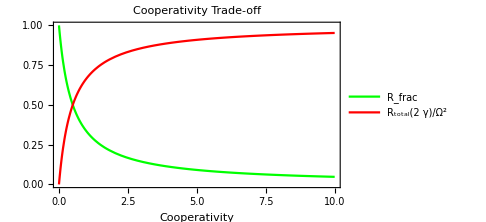

```mathematica
rTotal = 1/(1+2 coop);(*total atomic emission, Ω^2/γ = 1*)
rFrac = (2 coop)/(1+ 2 coop);(*fraction of emission into the cavity mode*)
plt=Plot[{rTotal,rFrac},{coop,0,10},PlotLegends->{"R_frac","R_total(2  γ)/Ω^2"}, PlotLabel->"Cooperativity Trade-off",FrameLabel->{"Cooperativity"}, ImageSize->Medium,PlotStyle->{Green,Red}]
```

```mathematica
Export[FileNameJoin[{imagedir,"cooperativity_tradeoff.png"}],plt]
```

C:\Users\gothr\Documents\Graduate Research\Mathematica\atomic_physics\images\cooperativity_tradeoff.png

### Strong coupling regime

Rachel Holdy thesis: both m0 and N0 should be < 1 for strong coupling.

```mathematica
"Critical photon number"
m0 = Γ^2/(2 g^2)(*critical photon number*)
"Critical atom number"
N0 = 1/Cooperativity (*critical atom number = 1/C*)
```

Critical photon number

0.00122235

Critical atom number

0.25178

### Enhanced emission

Feld paper. “The ratio of the spontaneous-emission rate into a single resonant cavity mode of quality factor Q and volume V to the total rate in free space is given by”

```mathematica
Q = (2π c/λ)/κ;
η=(3Q λ^3)/(4 π^2 V)(*depends only on solid angle and mirror reflectivity, not on λ/L*)
```

32.8078

## Atom collection - cavity vs free space

Comparison of photon collection from a single atom in a resonant cavity compared to an atom at the focus of a high NA lens. Also take into acct the overall rate of emission of the atom in the former case.

### ignoring atom perturbation

repeated pumping of the atom without a break for cooling may heat the push the atom out of the cavity mode volume or field of view of the lens; for now we will treat the atom as being stationary.

#### free space dipole emission pattern

```mathematica
λ = 7.8*10^-7;
k = 2π/λ;
unit[v_]:=v/(√(v.v));
(*GdotP[r_,p_]:=ⅇ^(ⅈ k √(r.r))/(4 π √(r.r))(Cross[Cross[unit[r],p],unit[r]]+(1/(k^2 r.r)-ⅈ/(k √(r.r)))(3unit[r] Dot[unit[r],p]-p));*)
```

spherical basis r, θ, ϕ. From Stephenson thesis, un-normalized polarization state. integration below freaks out and gives a bizarre result if i normalize the states.

```mathematica
pi ={0,-Sin[θ],0};
rh =ⅇ^(ⅈ ϕ)/(√2){0,Cos[θ],ⅈ};
lh =ⅇ^(-ⅈ ϕ)/(√2){0,Cos[θ],-ⅈ};
```

Verify that the three states give equal contribution of polarization

```mathematica
Map[Integrate[#.conj[#] Sin[θ],{θ,0,π},{ϕ,0,2π}]&,{pi,lh,rh}]
```

{(8 π)/3,(8 π)/3,(8 π)/3}

```mathematica
norm = 1/%[[1]]
```

3/(8 π)

Verify the states are orthogonal

```mathematica
Integrate[rh.conj[pi] Sin[θ],{θ,0,π},{ϕ,0,2π}]
Integrate[lh.conj[pi] Sin[θ],{θ,0,π},{ϕ,0,2π}]
Integrate[lh.conj[rh] Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

0

0

0

```mathematica
plt=PolarPlot[{(lh.conj[lh]+rh.conj[rh])norm,pi.conj[pi]norm},{θ,0,2π},PlotLabel-> "Dipole emission pattern",PlotLegends->{"P(σ+ or σ-)","P(π)"},PlotStyle->{Green,Red}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{imagedir,"dipole_emission.png"}],plt]
```

C:\Users\gothr\Documents\Graduate Research\Mathematica\atomic_physics\images\dipole_emission.png

The percentage of emitted circularly polarized photons which are collected by the lens is given by:

```mathematica
NA = 0.6;
θlens =ArcSin[0.6];
Psigma=norm Integrate[lh.conj[lh]Sin[θ],{θ,0,θlens},{ϕ,0,2π}]
```

0.136

The fraction of emitted linear photons, which we do not want, but collect nonetheless is given by:

```mathematica
Plinear = norm Integrate[pi.conj[pi]Sin[θ],{θ,0,θlens},{ϕ,0,2π}]
```

0.028

For the Rb D2 line F=0-> F=1 transition, with equal branching ratios among hyperfine states, 2/3 of the photons will be σ polarized, and hence the photons we want and those we do not have relative collection probabilities (normalized to total emission):

```mathematica
2/3 Psigma
```

0.0906667

```mathematica
1/3 Plinear
```

0.00933333

Sanity check: a 0.6 NA lens spans 10% of the solid angle, so we should collect 10% of all emission:

```mathematica
2/3 Psigma+1/3 Plinear
```

0.1

Taking into account fiber coupling efficiency η, the probability of reading a σ photon out of the fiber is

```mathematica
η = 0.9;
PCollect=η 2/3 Psigma (*the probability of collecting a σ photon in the fiber. this is what we want to beat with a cavity*)
```

0.0816

```mathematica
contrast = (2/3 Psigma -1/3 Pcollect)/(2/3 Psigma +1/3 Pcollect)
```

0.5

#### fiber resonator collection

if a fiber resonator is not birefringent, the Purcell effect should act equally on all polarization states.

If the cavity is being weakly driven by an external field: The fractional emission goes up with cooperativity while the total emission goes down, so that the total emission collected by one end of the fiber resonator is

```mathematica
rTotal = ξ 1/(1+2 coop);(*total atomic emission, ξ=Ω^2/γ *)
rFrac = (2 coop)/(1+ 2 coop);(*fraction of emission into the cavity mode*)
PCollect = 2/3 Psigma rTotal rFrac
```

(0.181333 coop ξ)/(1+2 coop)^2

However if we are simply going to excite the atom and let it decay, the situation is a little different. The rate of spontaneous emission can actually be enhanced by a high Q cavity.

```mathematica
ηenh = (3Q)/(4 π^2)λ^3/V;(*Q, V the cavity quality and mode volume*)
```

Check the Feld paper’s expression to see if equation 1 is consistent with the enhancement factor.

## Single atom detection

### Resonant detection

Don’t care about how many photons required to detect the atom for small pump powers (large powers could heat the atom out of the detection region), but want N0 small, ~ 1. (Holdy thesis)

For an atom in a cavity, the absorption cross section scales as 1/mode area. For a coherent state illuminating the cavity, with mean photon number N0, we are trying to detect a change ΔN = N0 - N = N0 σ/ A.

#### Transmission SNR

Haase thesis derives an SNR formula which depends on the mean number of photons in the cavity: (eq 3.30, from steady state solution of Jaynes-Cummings treatment). Below I reproduce some relevant figures.

```mathematica
Clear[g,Γ,κ,n]
```

```mathematica
γ=(g^2 Γ)/(Γ^2+Δa^2+2 g^2 n);(*additional decay rate due to spontaneous scattering*)
U=(g^2 Δa)/(Γ^2+Δa^2+2 g^2 n);(*phase shift due to coherent scattering*)
η^2/((κ+γ)^2+(Δc-U)^2);(*implicit expression for mean number of photons. η is the cavity pumping rate, = Subscript[η, in] Subscript[t, 1], rate of incident photons times the input mirror transmission*)
```

Reproduce figure 3.3b from Haase thesis. jIn is photon flux/μs:

```mathematica
Clear[κT];
κlo=2π 6*10^6;
κ=κT+κlo;(*cavity losses from mirrors + scattering to other modes*)
g=2π *12*^6; (*vacuum Rabi frequency*)
Γ=ΓD2/2 ;(*they are using 87Rb D2 line, and their Γ is the half-width*)
τ=10^-5;(*measurement interval*)
steps=2π*10^6{0.8,1.5,2.3,3.1,3.8,7.7};(*κT steps in s^-1*)
data = {};
For[i=1,i<Length[steps]+1,i++,
κT=steps[[i]];
AppendTo[data,Table[{jIn,√(jIn *10^6 τ)κT/κ(1+γ/κ-1/(1+γ/κ))/.{Δa-> 0,Δc-> 0,n->NSolve[n==η^2/((κ+γ)^2+(Δc-U)^2)/.{Δa-> 0,Δc-> 0,η ->√(jIn*10^6 κT)},n,Reals][[1,1,2]]}},{jIn, Range[0,400,10]}]];
]
```

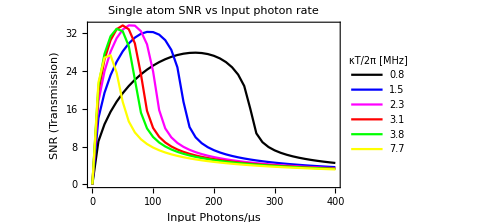

```mathematica
plt=ListPlot[data,PlotLabel-> "Single atom SNR vs Input photon rate",Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black,FontSize-> 14],FrameLabel->{"Input Photons/μs","SNR (Transmission)"},PlotLegends->PointLegend[steps/(2π*10^6),LegendLabel-> "κT/2π [MHz]",LegendFunction->"Frame"],Joined->True,PlotStyle->{Black,Blue,Magenta,Red,Green,Yellow},ImageSize->Medium]
```

```mathematica
fname=FileNameJoin[{imagedir,"plot_haase_fig3pt3_.png"}];
Export[fname,plt];
```

Reproduce fig. 3.4 from Haase thesis. Similar to above but with broader cavity linewidth due to internal losses.

```mathematica
g=2π *12*^6; (*vacuum Rabi frequency*)
Γ=ΓD2/2 ;(*they are using 87Rb D2 line, and their Γ is the half-width*)
τ=10^-5;(*measurement interval*)
steps=2π*10^6{6,20,50,100,200,500};(*κlo steps in s^-1*)
data = {};
For[i=1,i<Length[steps]+1,i++,
κlo=steps[[i]];
κT = κlo/2;(*"mirror transmission rate was chosen to be optimal for every curve"*)
κ=κT+κlo;
AppendTo[data,Table[{jIn,√(jIn *10^6 τ)κT/κ(1+γ/κ-1/(1+γ/κ))/.{Δa-> 0,Δc-> 0,n->NSolve[n==η^2/((κ+γ)^2+(Δc-U)^2)/.{Δa-> 0,Δc-> 0,η ->√(jIn*10^6 κT)},n,Reals][[1,1,2]]}},{jIn, {0.25,0.5,1,2.5,5,10,25,50,75,100,250,500,1000,2500,5000,10000}}]];
]
```

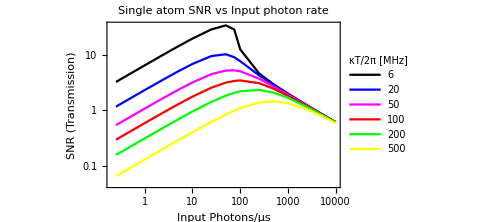

```mathematica
plt=ListLogLogPlot[data,PlotLabel-> "Single atom SNR vs Input photon rate",Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black,FontSize-> 14],FrameLabel->{"Input Photons/μs","SNR (Transmission)"},PlotLegends->PointLegend[steps/(2π*10^6),LegendLabel-> "κT/2π [MHz]",LegendFunction->"Frame"],Joined->True,PlotStyle->{Black,Blue,Magenta,Red,Green,Yellow},ImageSize->Medium]
```

```mathematica
fname=FileNameJoin[{imagedir,"plot_haase_fig3pt4_.png"}];
Export[fname,plt];
```

```mathematica
NSolve[n==η^2/((κ+γ)^2+(Δc-U)^2)/.{Δa-> 0,Δc-> 0,η ->√(50*10^6 κT)},n,Reals]
```

{{n→0.00508289}}

Find transmission SNR for our cavity parameters

Obtain mean intra-cavity photon number numerically (run one of the cavity sections above to initialize g, Γ, κ):

```mathematica
Table[NSolve[n==η^2/((κ+γ)^2+(Δc-U)^2)/.{Δa-> 0,Δc-> 0,η -> √(κ (P 7.8*^-7)/(ℏ 2π c))},n],{P,{10^-9,10^-8,10^-7,10^-6,10^-4,10^-3}}](*mean photon number in cavity for different laser powers. the pump rate η is √(cavity decay rate *incident photons/s)*)
```

{{{n→0.497362},{n→-0.0012224+0.000120191 ⅈ},{n→-0.0012224-0.000120191 ⅈ}},{{n→5.01731},{n→-0.00122235+0.0000378837 ⅈ},{n→-0.00122235-0.0000378837 ⅈ}},{{n→50.2168},{n→-0.00122235+0.000011976 ⅈ},{n→-0.00122235-0.000011976 ⅈ}},{{n→502.211},{n→-0.00122235+3.78701×10^-6 ⅈ},{n→-0.00122235-3.78701×10^-6 ⅈ}},{{n→50221.6},{n→-0.00122235+3.787×10^-7 ⅈ},{n→-0.00122235-3.787×10^-7 ⅈ}},{{n→502216.},{n→-0.00122235+1.19755×10^-7 ⅈ},{n→-0.00122235-1.19755×10^-7 ⅈ}}}

Photon number exiting cavity in measurement duration τ:

```mathematica
10^19*κ *10^-6
```

7.85058×10^22

Mean rate of photons/s for coherent field with power P:

```mathematica
((10^-9 J/s)(7.8*10^-7 m))/((ℏ J s)(2π c m/s))*(1 s)/(10^6 μs)
```

3942.69/μs

Signal-to-noise ratio in units √(n_(out,0)), the sqrt of number of photons read out of an empty cavity:

plot this for several points. need to find n numerically at each step in power. try to produce something similar to figure 3.4 in Haase thesis

```mathematica
1+γ/κ-1/(1+γ/κ)/.{Δa-> 0,Δc-> 0,η -> √(κ (P 7.8*^-7)/(ℏ 2π c)),n-> get numerically}
```

9.70964×10^-7

### Non-resonant detection

## Atomic ensemble in cavity

### Short confocal resonator - W state

How does the cooperativity factor change for an ensemble of atoms if we assume an effect two level state with the upper level being a W state excitation? The atomic decay rate is now enhanced, as the transition strength goes like √N for N atoms. Check this. Larger Γ_eff  -> lower cooperativity. However, g also goes like √N, so the cooperativity is unchanged.

Parameters for “gen 3” of the fiber Fabry-Perot built by the Goldsmith group.

```mathematica
(*CAVITY PARAMS*)
L=1.2*^-4;(*cavity length*)
RoC = 2.475*^-4;(*ablated fiber mirror radius of curvature*)
F =8.3*^3;(*cavity finesse, measured by Garrett 2019.07.26*)
FSR = c/(2L);(*free spectral range*)
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = √((λ L)/(2 π));(*Confocal waist*)
V = (π w0^2 L)/2;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/2π}
(*ATOM PARAMS*)
n = 10; (*atom number*)
d = D2MatElem; 
Γ =ΓD2; (*atom decay rate, e.g. 87Rb 5P3/2*)
λ =λD2;
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, confocal [dimensionless]:"
Cooperativity = 8/(ℏ ϵ0)(d^2 F)/(Γ λ^2 L)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)
```

Cavity w0, L, F, FSR, κ/(2π):

{3.86025×10^-6,0.00012,8300.,1.24946×10^12,1.48574×10^9}

Atom d [a.u.], Γ/(2π), λ:

{4.2344,6.0659×10^6,7.80241×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

1.22683×10^8

Cooperativity, confocal [dimensionless]:

3.29653

Fractional emission into cavity mode:

0.868301

Quantum efficiency:

0.834668

Compare w/ Mark’s result:

```mathematica
Cooperativity/23.9
```

1.0124

```mathematica
g/(2π 4.92*^7)
```

0.991048